### Examples using change of variables

```mathematica
Manipulate[{∫_0^t ⅇ^-x ⅆx,∫_0^t 2y ⅇ^(-y^2)ⅆy},{t,0,10}]
```

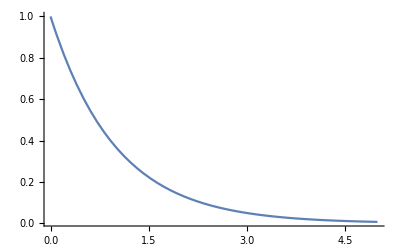

```mathematica
Plot[ⅇ^-x,{x,0,5},PlotRange->All]
```

```mathematica
∫_0^t 2y ⅇ^(-y^2)ⅆy
```

1-ⅇ^(-t^2)

```mathematica
y^2=x
```

```mathematica
2y dy/dx=1
```

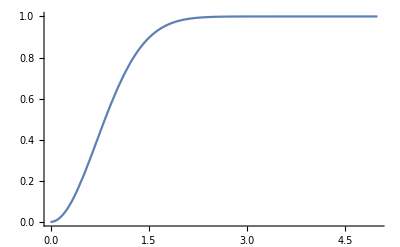

```mathematica
Plot[1-ⅇ^(-t^2),{t,0,5},PlotRange->All]
```

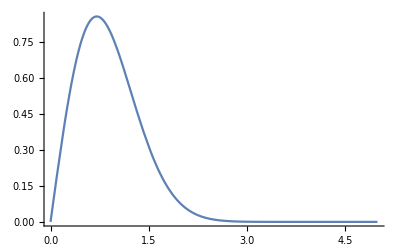

```mathematica
Plot[2y ⅇ^(-y^2),{y,0,5},PlotRange->All]
```

### “Two Moons” data

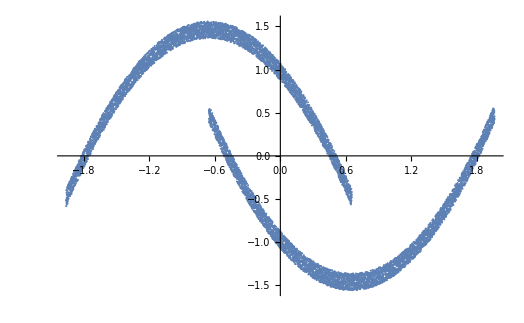

```mathematica
points=10000;
noise=0.1;
k=4/(points-2);
data=Standardize[Join[Table[{x,-2(x+0.5)^2+1.5+RandomReal[{-noise,noise}]},{x,-1.5,0.5,k}],Table[{x,2(x-0.5)^2-1.5+RandomReal[{-noise,noise}]},{x,-0.5,1.5,k}]]];
ListPlot@data
```

```mathematica
data=Standardize[Join[Table[{x,-2(x+0.5)^2+1.5+RandomReal[{-noise,noise}]},{x,-1.5,0.5,k}],Table[{x,2(x-0.5)^2-1.5+RandomReal[{-noise,noise}]},{x,-0.5,1.5,k}]]];
ListPlot@data
```

### LearnDistribution with Real-NVP

```mathematica
ld=LearnDistribution[data,Method->{"RealNVP","NetworkDepth"->8,"CouplingLayersNumber"->4,"ActivationFunction"->Ramp,MaxTrainingRounds->500},PerformanceGoal->"DirectTraining"]
```

LearnedDistribution[…]

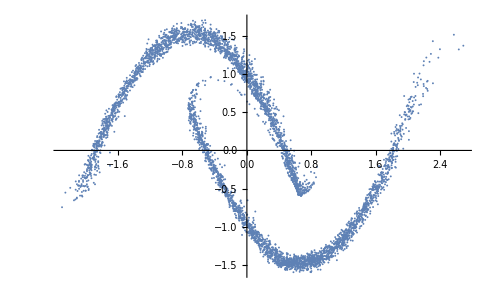

```mathematica
ListPlot@RandomVariate[ld,5000]
```

```mathematica
Show[ContourPlot[PDF[ld,{x,y}],{x,-2,2},{y,-2,2},PlotRange->All],ListPlot[data, PlotStyle->Red]]
```

$Aborted

```mathematica
ld[[1,"Model"]]
```

<|Sampler→NetGraph[<>],Processor→Center,PostProcessor→FirstValues,ProbabilityNet→NetGraph[<>],Method→RealNVP,Options→<|MaxTrainingRounds→<|Value→500,Options→<||>|>,ActivationFunction→<|Value→Ramp,Options→<||>|>,NetworkDepth→<|Value→8,Options→<||>|>,CouplingLayersNumber→<|Value→4,Options→<||>|>,NetworkType→<|Value→FullyConnected,Options→<||>|>|>|>

```mathematica
PDF[ld]
```

PDF[LearnedDistribution[…]]

```mathematica
ContourPlot[PDF[ld,{x,y}],{x,-2,2},{y,-2,2},PlotRange->All]
```

$Aborted